Defining STA Solutions

```mathematica
bsta[t_]=c0+c1 t+c2 t^2+c3 t^3+c4 t^4+c5 t^5 + c6 t^6
```

c0+c1 t+c2 t^2+c3 t^3+c4 t^4+c5 t^5+c6 t^6

```mathematica
solsta = Solve[{bsta[0]==1,bsta'[0]==0,bsta''[0]==0,bsta[tf]==gam,bsta'[tf]==0,bsta''[tf]== 0,bsta[tf/2]==beta},{c0,c1,c2,c3,c4,c5,c6}]
```

{{c0→1,c1→0,c2→0,c3→(2 (-21+32 beta-11 gam))/tf^3,c4→-(3 (-37+64 beta-27 gam))/tf^4,c5→(6 (-17+32 beta-15 gam))/tf^5,c6→-(32 (-1+2 beta-gam))/tf^6}}

```mathematica
gam=.
```

```mathematica
Solve[-(32 (-1+2 beta-gam))/tf^6==0,beta]
```

{{beta→(1+gam)/2}}

```mathematica
bsta[t_]=bsta[t]/.solsta[[1]]
```

1-(32 (-1+2 beta-gam) t^6)/tf^6+(6 (-17+32 beta-15 gam) t^5)/tf^5-(3 (-37+64 beta-27 gam) t^4)/tf^4+(2 (-21+32 beta-11 gam) t^3)/tf^3

```mathematica
bsta[tf/2]
```

1-3/16 (-37+64 beta-27 gam)+3/16 (-17+32 beta-15 gam)+1/4 (-21+32 beta-11 gam)+1/2 (1-2 beta+gam)

```mathematica
omsta2[t_]= ((omsta0^2)/(bsta[t]^4)- (bsta''[t])/bsta[t])//FullSimplify
```

(omsta0^2 tf^24)/((32 (1-2 beta+gam) t^6+6 (-17+32 beta-15 gam) t^5 tf+3 (37-64 beta+27 gam) t^4 tf^2+2 (-21+32 beta-11 gam) t^3 tf^3+tf^6)^4)+(12 t (t-tf) (80 (-1+2 beta-gam) t^2+10 (9-16 beta+7 gam) t tf+(-21+32 beta-11 gam) tf^2))/(32 (1-2 beta+gam) t^6+6 (-17+32 beta-15 gam) t^5 tf+3 (37-64 beta+27 gam) t^4 tf^2+2 (-21+32 beta-11 gam) t^3 tf^3+tf^6)

Defining Omega

```mathematica
deltaom[t_]= c0 +c1*t+c2*t^2+c3*t^3
```

c0+c1 t+c2 t^2+c3 t^3

```mathematica
sol=Solve[{deltaom[0]== 0,deltaom[tf]== 0,deltaom[tf/3]==a1,deltaom[2tf/3]==a2}, {c0, c1, c2,c3}]
```

{{c0→0,c1→(9 (2 a1-a2))/(2 tf),c2→-(9 (5 a1-4 a2))/(2 tf^2),c3→(27 (a1-a2))/(2 tf^3)}}

```mathematica
deltaomx[t_]=deltaom[t]/.sol[[1]]
```

(27 (a1-a2) t^3)/(2 tf^3)-(9 (5 a1-4 a2) t^2)/(2 tf^2)+(9 (2 a1-a2) t)/(2 tf)

```mathematica
om2[t_]=omsta2[t]+deltaomx[t]
```

(27 (a1-a2) t^3)/(2 tf^3)-(9 (5 a1-4 a2) t^2)/(2 tf^2)+(9 (2 a1-a2) t)/(2 tf)+(omsta0^2 tf^24)/((32 (1-2 beta+gam) t^6+6 (-17+32 beta-15 gam) t^5 tf+3 (37-64 beta+27 gam) t^4 tf^2+2 (-21+32 beta-11 gam) t^3 tf^3+tf^6)^4)+(12 t (t-tf) (80 (-1+2 beta-gam) t^2+10 (9-16 beta+7 gam) t tf+(-21+32 beta-11 gam) tf^2))/(32 (1-2 beta+gam) t^6+6 (-17+32 beta-15 gam) t^5 tf+3 (37-64 beta+27 gam) t^4 tf^2+2 (-21+32 beta-11 gam) t^3 tf^3+tf^6)

```mathematica
om2[t_]=omsta2[t]*(1+deltaomx[t])
```

(1+(27 (a1-a2) t^3)/(2 tf^3)-(9 (5 a1-4 a2) t^2)/(2 tf^2)+(9 (2 a1-a2) t)/(2 tf)) ((omsta0^2 tf^24)/((32 (1-2 beta+gam) t^6+6 (-17+32 beta-15 gam) t^5 tf+3 (37-64 beta+27 gam) t^4 tf^2+2 (-21+32 beta-11 gam) t^3 tf^3+tf^6)^4)+(12 t (t-tf) (80 (-1+2 beta-gam) t^2+10 (9-16 beta+7 gam) t tf+(-21+32 beta-11 gam) tf^2))/(32 (1-2 beta+gam) t^6+6 (-17+32 beta-15 gam) t^5 tf+3 (37-64 beta+27 gam) t^4 tf^2+2 (-21+32 beta-11 gam) t^3 tf^3+tf^6))

Defining Fidelities

```mathematica
eq=b''[t] == (om0^2)/(b[t]^3)- om2[t]*b[t]  
gam  = (om0/omf)^0.5
Fid[bf_,bfdot_]= ((4*om0^2*bf^2*gam^2)/((om0^2*(gam^2+bf^2)^2)+(bfdot*bf*gam^2)^2))^0.5
```

b''[t]==om0^2/b[t]^3-(1+(27 (a1-a2) t^3)/(2 tf^3)-(9 (5 a1-4 a2) t^2)/(2 tf^2)+(9 (2 a1-a2) t)/(2 tf)) ((omsta0^2 tf^24)/((32 (1-2 beta+gam) t^6+6 (-17+32 beta-15 gam) t^5 tf+3 (37-64 beta+27 gam) t^4 tf^2+2 (-21+32 beta-11 gam) t^3 tf^3+tf^6)^4)+(12 t (t-tf) (80 (-1+2 beta-gam) t^2+10 (9-16 beta+7 gam) t tf+(-21+32 beta-11 gam) tf^2))/(32 (1-2 beta+gam) t^6+6 (-17+32 beta-15 gam) t^5 tf+3 (37-64 beta+27 gam) t^4 tf^2+2 (-21+32 beta-11 gam) t^3 tf^3+tf^6)) b[t]

(om0/omf)^0.5

2. ((bf^2 om0^2 (om0/omf)^1.)/(om0^2 (bf^2+(om0/omf)^1.)^2+bf^2 bfdot^2 (om0/omf)^2.))^0.5

```mathematica
om0=1
omsta0 =om0
omf=0.1
(*tf=1*)
```

1

1

0.1

Calculating Fidelities from List of a1 & a2 Values

```mathematica
list1=Flatten[Table[{a1,a2},{a1,-0.5,0.5,0.05},{a2,-0.5,0.5,0.05}],1]
```

{{-0.5,-0.5},{-0.5,-0.45},{-0.5,-0.4},{-0.5,-0.35},{-0.5,-0.3},{-0.5,-0.25},{-0.5,-0.2},{-0.5,-0.15},{-0.5,-0.1},{-0.5,-0.05},{-0.5,0.},{-0.5,0.05},{-0.5,0.1},{-0.5,0.15},{-0.5,0.2},{-0.5,0.25},{-0.5,0.3},{-0.5,0.35},{-0.5,0.4},{-0.5,0.45},{-0.5,0.5},{-0.45,-0.5},{-0.45,-0.45},{-0.45,-0.4},{-0.45,-0.35},{-0.45,-0.3},{-0.45,-0.25},{-0.45,-0.2},{-0.45,-0.15},{-0.45,-0.1},{-0.45,-0.05},{-0.45,0.},{-0.45,0.05},{-0.45,0.1},{-0.45,0.15},{-0.45,0.2},{-0.45,0.25},{-0.45,0.3},{-0.45,0.35},{-0.45,0.4},{-0.45,0.45},{-0.45,0.5},{-0.4,-0.5},{-0.4,-0.45},{-0.4,-0.4},{-0.4,-0.35},{-0.4,-0.3},{-0.4,-0.25},{-0.4,-0.2},{-0.4,-0.15},{-0.4,-0.1},{-0.4,-0.05},{-0.4,0.},{-0.4,0.05},{-0.4,0.1},{-0.4,0.15},{-0.4,0.2},{-0.4,0.25},{-0.4,0.3},{-0.4,0.35},{-0.4,0.4},{-0.4,0.45},{-0.4,0.5},{-0.35,-0.5},{-0.35,-0.45},{-0.35,-0.4},{-0.35,-0.35},{-0.35,-0.3},{-0.35,-0.25},{-0.35,-0.2},{-0.35,-0.15},{-0.35,-0.1},{-0.35,-0.05},{-0.35,0.},{-0.35,0.05},{-0.35,0.1},{-0.35,0.15},{-0.35,0.2},{-0.35,0.25},{-0.35,0.3},{-0.35,0.35},{-0.35,0.4},{-0.35,0.45},{-0.35,0.5},{-0.3,-0.5},{-0.3,-0.45},{-0.3,-0.4},{-0.3,-0.35},{-0.3,-0.3},{-0.3,-0.25},{-0.3,-0.2},{-0.3,-0.15},{-0.3,-0.1},{-0.3,-0.05},{-0.3,0.},{-0.3,0.05},{-0.3,0.1},{-0.3,0.15},{-0.3,0.2},{-0.3,0.25},{-0.3,0.3},{-0.3,0.35},{-0.3,0.4},{-0.3,0.45},{-0.3,0.5},{-0.25,-0.5},{-0.25,-0.45},{-0.25,-0.4},{-0.25,-0.35},{-0.25,-0.3},{-0.25,-0.25},{-0.25,-0.2},{-0.25,-0.15},{-0.25,-0.1},{-0.25,-0.05},{-0.25,0.},{-0.25,0.05},{-0.25,0.1},{-0.25,0.15},{-0.25,0.2},{-0.25,0.25},{-0.25,0.3},{-0.25,0.35},{-0.25,0.4},{-0.25,0.45},{-0.25,0.5},{-0.2,-0.5},{-0.2,-0.45},{-0.2,-0.4},{-0.2,-0.35},{-0.2,-0.3},{-0.2,-0.25},{-0.2,-0.2},{-0.2,-0.15},{-0.2,-0.1},{-0.2,-0.05},{-0.2,0.},{-0.2,0.05},{-0.2,0.1},{-0.2,0.15},{-0.2,0.2},{-0.2,0.25},{-0.2,0.3},{-0.2,0.35},{-0.2,0.4},{-0.2,0.45},{-0.2,0.5},{-0.15,-0.5},{-0.15,-0.45},{-0.15,-0.4},{-0.15,-0.35},{-0.15,-0.3},{-0.15,-0.25},{-0.15,-0.2},{-0.15,-0.15},{-0.15,-0.1},{-0.15,-0.05},{-0.15,0.},{-0.15,0.05},{-0.15,0.1},{-0.15,0.15},{-0.15,0.2},{-0.15,0.25},{-0.15,0.3},{-0.15,0.35},{-0.15,0.4},{-0.15,0.45},{-0.15,0.5},{-0.1,-0.5},{-0.1,-0.45},{-0.1,-0.4},{-0.1,-0.35},{-0.1,-0.3},{-0.1,-0.25},{-0.1,-0.2},{-0.1,-0.15},{-0.1,-0.1},{-0.1,-0.05},{-0.1,0.},{-0.1,0.05},{-0.1,0.1},{-0.1,0.15},{-0.1,0.2},{-0.1,0.25},{-0.1,0.3},{-0.1,0.35},{-0.1,0.4},{-0.1,0.45},{-0.1,0.5},{-0.05,-0.5},{-0.05,-0.45},{-0.05,-0.4},{-0.05,-0.35},{-0.05,-0.3},{-0.05,-0.25},{-0.05,-0.2},{-0.05,-0.15},{-0.05,-0.1},{-0.05,-0.05},{-0.05,0.},{-0.05,0.05},{-0.05,0.1},{-0.05,0.15},{-0.05,0.2},{-0.05,0.25},{-0.05,0.3},{-0.05,0.35},{-0.05,0.4},{-0.05,0.45},{-0.05,0.5},{0.,-0.5},{0.,-0.45},{0.,-0.4},{0.,-0.35},{0.,-0.3},{0.,-0.25},{0.,-0.2},{0.,-0.15},{0.,-0.1},{0.,-0.05},{0.,0.},{0.,0.05},{0.,0.1},{0.,0.15},{0.,0.2},{0.,0.25},{0.,0.3},{0.,0.35},{0.,0.4},{0.,0.45},{0.,0.5},{0.05,-0.5},{0.05,-0.45},{0.05,-0.4},{0.05,-0.35},{0.05,-0.3},{0.05,-0.25},{0.05,-0.2},{0.05,-0.15},{0.05,-0.1},{0.05,-0.05},{0.05,0.},{0.05,0.05},{0.05,0.1},{0.05,0.15},{0.05,0.2},{0.05,0.25},{0.05,0.3},{0.05,0.35},{0.05,0.4},{0.05,0.45},{0.05,0.5},{0.1,-0.5},{0.1,-0.45},{0.1,-0.4},{0.1,-0.35},{0.1,-0.3},{0.1,-0.25},{0.1,-0.2},{0.1,-0.15},{0.1,-0.1},{0.1,-0.05},{0.1,0.},{0.1,0.05},{0.1,0.1},{0.1,0.15},{0.1,0.2},{0.1,0.25},{0.1,0.3},{0.1,0.35},{0.1,0.4},{0.1,0.45},{0.1,0.5},{0.15,-0.5},{0.15,-0.45},{0.15,-0.4},{0.15,-0.35},{0.15,-0.3},{0.15,-0.25},{0.15,-0.2},{0.15,-0.15},{0.15,-0.1},{0.15,-0.05},{0.15,0.},{0.15,0.05},{0.15,0.1},{0.15,0.15},{0.15,0.2},{0.15,0.25},{0.15,0.3},{0.15,0.35},{0.15,0.4},{0.15,0.45},{0.15,0.5},{0.2,-0.5},{0.2,-0.45},{0.2,-0.4},{0.2,-0.35},{0.2,-0.3},{0.2,-0.25},{0.2,-0.2},{0.2,-0.15},{0.2,-0.1},{0.2,-0.05},{0.2,0.},{0.2,0.05},{0.2,0.1},{0.2,0.15},{0.2,0.2},{0.2,0.25},{0.2,0.3},{0.2,0.35},{0.2,0.4},{0.2,0.45},{0.2,0.5},{0.25,-0.5},{0.25,-0.45},{0.25,-0.4},{0.25,-0.35},{0.25,-0.3},{0.25,-0.25},{0.25,-0.2},{0.25,-0.15},{0.25,-0.1},{0.25,-0.05},{0.25,0.},{0.25,0.05},{0.25,0.1},{0.25,0.15},{0.25,0.2},{0.25,0.25},{0.25,0.3},{0.25,0.35},{0.25,0.4},{0.25,0.45},{0.25,0.5},{0.3,-0.5},{0.3,-0.45},{0.3,-0.4},{0.3,-0.35},{0.3,-0.3},{0.3,-0.25},{0.3,-0.2},{0.3,-0.15},{0.3,-0.1},{0.3,-0.05},{0.3,0.},{0.3,0.05},{0.3,0.1},{0.3,0.15},{0.3,0.2},{0.3,0.25},{0.3,0.3},{0.3,0.35},{0.3,0.4},{0.3,0.45},{0.3,0.5},{0.35,-0.5},{0.35,-0.45},{0.35,-0.4},{0.35,-0.35},{0.35,-0.3},{0.35,-0.25},{0.35,-0.2},{0.35,-0.15},{0.35,-0.1},{0.35,-0.05},{0.35,0.},{0.35,0.05},{0.35,0.1},{0.35,0.15},{0.35,0.2},{0.35,0.25},{0.35,0.3},{0.35,0.35},{0.35,0.4},{0.35,0.45},{0.35,0.5},{0.4,-0.5},{0.4,-0.45},{0.4,-0.4},{0.4,-0.35},{0.4,-0.3},{0.4,-0.25},{0.4,-0.2},{0.4,-0.15},{0.4,-0.1},{0.4,-0.05},{0.4,0.},{0.4,0.05},{0.4,0.1},{0.4,0.15},{0.4,0.2},{0.4,0.25},{0.4,0.3},{0.4,0.35},{0.4,0.4},{0.4,0.45},{0.4,0.5},{0.45,-0.5},{0.45,-0.45},{0.45,-0.4},{0.45,-0.35},{0.45,-0.3},{0.45,-0.25},{0.45,-0.2},{0.45,-0.15},{0.45,-0.1},{0.45,-0.05},{0.45,0.},{0.45,0.05},{0.45,0.1},{0.45,0.15},{0.45,0.2},{0.45,0.25},{0.45,0.3},{0.45,0.35},{0.45,0.4},{0.45,0.45},{0.45,0.5},{0.5,-0.5},{0.5,-0.45},{0.5,-0.4},{0.5,-0.35},{0.5,-0.3},{0.5,-0.25},{0.5,-0.2},{0.5,-0.15},{0.5,-0.1},{0.5,-0.05},{0.5,0.},{0.5,0.05},{0.5,0.1},{0.5,0.15},{0.5,0.2},{0.5,0.25},{0.5,0.3},{0.5,0.35},{0.5,0.4},{0.5,0.45},{0.5,0.5}}

```mathematica
a1=.
a2=.
```

```mathematica
eq
```

b''[t]==1/b[t]^3-(1+(27 (a1-a2) t^3)/(2 tf^3)-(9 (5 a1-4 a2) t^2)/(2 tf^2)+(9 (2 a1-a2) t)/(2 tf)) (tf^24/((32 (4.16228-2 beta) t^6+6 (-64.4342+32 beta) t^5 tf+3 (122.381-64 beta) t^4 tf^2+2 (-55.7851+32 beta) t^3 tf^3+tf^6)^4)+(12 t (t-tf) (80 (-4.16228+2 beta) t^2+10 (31.1359-16 beta) t tf+(-55.7851+32 beta) tf^2))/(32 (4.16228-2 beta) t^6+6 (-64.4342+32 beta) t^5 tf+3 (122.381-64 beta) t^4 tf^2+2 (-55.7851+32 beta) t^3 tf^3+tf^6)) b[t]

```mathematica
Fidtable2[be_]:=
Module[{},
beta=be;
Table[{list1[[nr]][[1]],list1[[nr]][[2]],
a1=list1[[nr]][[1]];
a2=list1[[nr]][[2]];
om0= 1;
omsta0=om0;
omf=0.1;
tf=2;
sol=NDSolve[{eq,b[0]==1,b'[0]==0},b[t],{t,0,tf}];
bsol[t_]=b[t]/.sol[[1]];
Fid[bsol[tf],bsol'[tf]]},{nr,1,Length[list1]}]
]
```

```mathematica
result=Fidtable2[(1+gam)/2.]
```

{{-0.5,-0.5,0.839846},{-0.5,-0.45,0.882271},{-0.5,-0.4,0.919752},{-0.5,-0.35,0.949717},{-0.5,-0.3,0.969857},{-0.5,-0.25,0.978637},{-0.5,-0.2,0.975673},{-0.5,-0.15,0.961814},{-0.5,-0.1,0.938877},{-0.5,-0.05,0.909189},{-0.5,0.,0.875122},{-0.5,0.05,0.838758},{-0.5,0.1,0.801742},{-0.5,0.15,0.765257},{-0.5,0.2,0.730086},{-0.5,0.25,0.696694},{-0.5,0.3,0.665322},{-0.5,0.35,0.636052},{-0.5,0.4,0.608866},{-0.5,0.45,0.583685},{-0.5,0.5,0.560393},{-0.45,-0.5,0.814879},{-0.45,-0.45,0.860299},{-0.45,-0.4,0.902138},{-0.45,-0.35,0.937697},{-0.45,-0.3,0.96426},{-0.45,-0.25,0.979637},{-0.45,-0.2,0.982705},{-0.45,-0.15,0.973697},{-0.45,-0.1,0.954104},{-0.45,-0.05,0.926239},{-0.45,0.,0.892692},{-0.45,0.05,0.855872},{-0.45,0.1,0.817753},{-0.45,0.15,0.779798},{-0.45,0.2,0.742993},{-0.45,0.25,0.707945},{-0.45,0.3,0.674978},{-0.45,0.35,0.644221},{-0.45,0.4,0.615677},{-0.45,0.45,0.589274},{-0.45,0.5,0.564893},{-0.4,-0.5,0.78817},{-0.4,-0.45,0.83577},{-0.4,-0.4,0.881184},{-0.4,-0.35,0.921745},{-0.4,-0.3,0.954487},{-0.4,-0.25,0.976659},{-0.4,-0.2,0.986368},{-0.4,-0.15,0.983083},{-0.4,-0.1,0.967766},{-0.4,-0.05,0.942548},{-0.4,0.,0.910149},{-0.4,0.05,0.87329},{-0.4,0.1,0.834309},{-0.4,0.15,0.794991},{-0.4,0.2,0.756577},{-0.4,0.25,0.719845},{-0.4,0.3,0.68523},{-0.4,0.35,0.652924},{-0.4,0.4,0.622962},{-0.4,0.45,0.595278},{-0.4,0.5,0.569755},{-0.35,-0.5,0.760263},{-0.35,-0.45,0.809245},{-0.35,-0.4,0.857384},{-0.35,-0.35,0.902182},{-0.35,-0.3,0.940606},{-0.35,-0.25,0.9695},{-0.35,-0.2,0.986246},{-0.35,-0.15,0.989455},{-0.35,-0.1,0.979362},{-0.35,-0.05,0.957711},{-0.35,0.,0.927208},{-0.35,0.05,0.890838},{-0.35,0.1,0.851315},{-0.35,0.15,0.810799},{-0.35,0.2,0.770831},{-0.35,0.25,0.732406},{-0.35,0.3,0.696099},{-0.35,0.35,0.662185},{-0.35,0.4,0.630739},{-0.35,0.45,0.601715},{-0.35,0.5,0.574995},{-0.3,-0.5,0.731662},{-0.3,-0.45,0.781286},{-0.3,-0.4,0.831291},{-0.3,-0.35,0.879458},{-0.3,-0.3,0.922857},{-0.3,-0.25,0.958117},{-0.3,-0.2,0.982029},{-0.3,-0.15,0.992331},{-0.3,-0.1,0.988368},{-0.3,-0.05,0.971264},{-0.3,0.,0.943522},{-0.3,0.05,0.908289},{-0.3,0.1,0.868646},{-0.3,0.15,0.827163},{-0.3,0.2,0.785739},{-0.3,0.25,0.745635},{-0.3,0.3,0.707603},{-0.3,0.35,0.672024},{-0.3,0.4,0.639031},{-0.3,0.45,0.608604},{-0.3,0.5,0.58063},{-0.25,-0.5,0.702814},{-0.25,-0.45,0.752426},{-0.25,-0.4,0.803483},{-0.25,-0.35,0.854111},{-0.25,-0.3,0.901624},{-0.25,-0.25,0.942642},{-0.25,-0.2,0.973556},{-0.25,-0.15,0.991311},{-0.25,-0.1,0.994266},{-0.25,-0.05,0.982703},{-0.25,0.,0.958685},{-0.25,0.05,0.925363},{-0.25,0.1,0.886132},{-0.25,0.15,0.843998},{-0.25,0.2,0.801269},{-0.25,0.25,0.75953},{-0.25,0.3,0.719754},{-0.25,0.35,0.68246},{-0.25,0.4,0.647859},{-0.25,0.45,0.615964},{-0.25,0.5,0.586675},{-0.2,-0.5,0.674096},{-0.2,-0.45,0.723148},{-0.2,-0.4,0.774523},{-0.2,-0.35,0.826723},{-0.2,-0.3,0.877408},{-0.2,-0.25,0.923374},{-0.2,-0.2,0.960836},{-0.2,-0.15,0.986111},{-0.2,-0.1,0.996579},{-0.2,-0.05,0.991501},{-0.2,0.,0.972234},{-0.2,0.05,0.941717},{-0.2,0.1,0.903557},{-0.2,0.15,0.861185},{-0.2,0.2,0.81737},{-0.2,0.25,0.77408},{-0.2,0.3,0.732563},{-0.2,0.35,0.693514},{-0.2,0.4,0.657243},{-0.2,0.45,0.623815},{-0.2,0.5,0.59315},{-0.15,-0.5,0.645816},{-0.15,-0.45,0.693864},{-0.15,-0.4,0.744927},{-0.15,-0.35,0.797878},{-0.15,-0.3,0.85078},{-0.15,-0.25,0.90075},{-0.15,-0.2,0.944051},{-0.15,-0.15,0.976606},{-0.15,-0.1,0.994919},{-0.15,-0.05,0.997137},{-0.15,0.,0.98366},{-0.15,0.05,0.956949},{-0.15,0.1,0.920646},{-0.15,0.15,0.878565},{-0.15,0.2,0.833965},{-0.15,0.25,0.789259},{-0.15,0.3,0.746032},{-0.15,0.35,0.705199},{-0.15,0.4,0.667203},{-0.15,0.45,0.632178},{-0.15,0.5,0.600071},{-0.1,-0.5,0.618212},{-0.1,-0.45,0.664916},{-0.1,-0.4,0.71515},{-0.1,-0.35,0.768129},{-0.1,-0.3,0.822339},{-0.1,-0.25,0.875308},{-0.1,-0.2,0.923549},{-0.1,-0.15,0.962842},{-0.1,-0.1,0.989023},{-0.1,-0.05,0.999138},{-0.1,0.,0.992436},{-0.1,0.05,0.970598},{-0.1,0.1,0.937069},{-0.1,0.15,0.895933},{-0.1,0.2,0.850945},{-0.1,0.25,0.805023},{-0.1,0.3,0.760152},{-0.1,0.35,0.717527},{-0.1,0.4,0.677759},{-0.1,0.45,0.641074},{-0.1,0.5,0.60746},{-0.05,-0.5,0.591462},{-0.05,-0.45,0.636575},{-0.05,-0.4,0.685572},{-0.05,-0.35,0.737974},{-0.05,-0.3,0.792668},{-0.05,-0.25,0.847645},{-0.05,-0.2,0.899808},{-0.05,-0.15,0.945044},{-0.05,-0.1,0.978788},{-0.05,-0.05,0.997123},{-0.05,0.,0.99804},{-0.05,0.05,0.982161},{-0.05,0.1,0.952431},{-0.05,0.15,0.913029},{-0.05,0.2,0.868165},{-0.05,0.25,0.821304},{-0.05,0.3,0.774906},{-0.05,0.35,0.730505},{-0.05,0.4,0.688928},{-0.05,0.45,0.650522},{-0.05,0.5,0.615335},{0.,-0.5,0.56569},{0.,-0.45,0.609043},{0.,-0.4,0.6565},{0.,-0.35,0.707838},{0.,-0.3,0.762308},{0.,-0.25,0.818365},{0.,-0.2,0.873394},{0.,-0.15,0.923595},{0.,-0.1,0.964292},{0.,-0.05,0.990839},{0.,0.,1.},{0.,0.05,0.991108},{0.,0.1,0.966282},{0.,0.15,0.929536},{0.,0.2,0.885435},{0.,0.25,0.838009},{0.,0.3,0.790258},{0.,0.35,0.74413},{0.,0.4,0.700723},{0.,0.45,0.660543},{0.,0.5,0.623717},{0.05,-0.5,0.540977},{0.05,-0.45,0.582468},{0.05,-0.4,0.628172},{0.05,-0.35,0.678071},{0.05,-0.3,0.731734},{0.05,-0.25,0.788049},{0.05,-0.2,0.844918},{0.05,-0.15,0.899003},{0.05,-0.1,0.945785},{0.05,-0.05,0.980199},{0.05,0.,0.997932},{0.05,0.05,0.996918},{0.05,0.1,0.978123},{0.05,0.15,0.945076},{0.05,0.2,0.902514},{0.05,0.25,0.855006},{0.05,0.3,0.806152},{0.05,0.35,0.758389},{0.05,0.4,0.713153},{0.05,0.45,0.671153},{0.05,0.5,0.632626},{0.1,-0.5,0.517366},{0.1,-0.45,0.556947},{0.1,-0.4,0.60076},{0.1,-0.35,0.64895},{0.1,-0.3,0.701345},{0.1,-0.25,0.757222},{0.1,-0.2,0.814989},{0.1,-0.15,0.871854},{0.1,-0.1,0.923676},{0.1,-0.05,0.965292},{0.1,0.,0.991586},{0.1,0.05,0.999114},{0.1,0.1,0.987429},{0.1,0.15,0.959211},{0.1,0.2,0.919104},{0.1,0.25,0.872125},{0.1,0.3,0.822507},{0.1,0.35,0.773256},{0.1,0.4,0.726221},{0.1,0.45,0.68237},{0.1,0.5,0.642081},{0.15,-0.5,0.494874},{0.15,-0.45,0.532538},{0.15,-0.4,0.574385},{0.15,-0.35,0.620682},{0.15,-0.3,0.671465},{0.15,-0.25,0.726339},{0.15,-0.2,0.78418},{0.15,-0.15,0.842768},{0.15,-0.1,0.898493},{0.15,-0.05,0.946387},{0.15,0.,0.980875},{0.15,0.05,0.997305},{0.15,0.1,0.993677},{0.15,0.15,0.971455},{0.15,0.2,0.934847},{0.15,0.25,0.889146},{0.15,0.3,0.83921},{0.15,0.35,0.788687},{0.15,0.4,0.739921},{0.15,0.45,0.694204},{0.15,0.5,0.652101},{0.2,-0.5,0.473495},{0.2,-0.45,0.509267},{0.2,-0.4,0.549122},{0.2,-0.35,0.593414},{0.2,-0.3,0.642342},{0.2,-0.25,0.695777},{0.2,-0.2,0.753003},{0.2,-0.15,0.812357},{0.2,-0.1,0.870835},{0.2,-0.05,0.923906},{0.2,0.,0.965892},{0.2,0.05,0.991231},{0.2,0.1,0.996383},{0.2,0.15,0.98129},{0.2,0.2,0.949325},{0.2,0.25,0.905794},{0.2,0.3,0.85611},{0.2,0.35,0.804614},{0.2,0.4,0.754234},{0.2,0.45,0.706662},{0.2,0.5,0.662703},{0.25,-0.5,0.453209},{0.25,-0.45,0.487135},{0.25,-0.4,0.52501},{0.25,-0.35,0.567246},{0.25,-0.3,0.614159},{0.25,-0.25,0.665833},{0.25,-0.2,0.721896},{0.25,-0.15,0.781185},{0.25,-0.1,0.841328},{0.25,-0.05,0.898387},{0.25,0.,0.946907},{0.25,0.05,0.980795},{0.25,0.1,0.995143},{0.25,0.15,0.988192},{0.25,0.2,0.962069},{0.25,0.25,0.921738},{0.25,0.3,0.873013},{0.25,0.35,0.820944},{0.25,0.4,0.769127},{0.25,0.45,0.719743},{0.25,0.5,0.6739},{0.3,-0.5,0.433983},{0.3,-0.45,0.466126},{0.3,-0.4,0.50206},{0.3,-0.35,0.542232},{0.3,-0.3,0.587042},{0.3,-0.25,0.636734},{0.3,-0.2,0.691214},{0.3,-0.15,0.749753},{0.3,-0.1,0.810582},{0.3,-0.05,0.870438},{0.3,0.,0.924345},{0.3,0.05,0.966077},{0.3,0.1,0.989679},{0.3,0.15,0.991668},{0.3,0.2,0.972572},{0.3,0.25,0.936585},{0.3,0.3,0.889672},{0.3,0.35,0.837547},{0.3,0.4,0.784548},{0.3,0.45,0.733438},{0.3,0.5,0.685704},{0.35,-0.5,0.415778},{0.35,-0.45,0.446211},{0.35,-0.4,0.480263},{0.35,-0.35,0.518398},{0.35,-0.3,0.561071},{0.35,-0.25,0.608644},{0.35,-0.2,0.661236},{0.35,-0.15,0.718484},{0.35,-0.1,0.779159},{0.35,-0.05,0.840688},{0.35,0.,0.898748},{0.35,0.05,0.947339},{0.35,0.1,0.979867},{0.35,0.15,0.991297},{0.35,0.2,0.980313},{0.35,0.25,0.949888},{0.35,0.3,0.905783},{0.35,0.35,0.854255},{0.35,0.4,0.800422},{0.35,0.45,0.747725},{0.35,0.5,0.698119},{0.4,-0.5,0.398548},{0.4,-0.45,0.427352},{0.4,-0.4,0.459593},{0.4,-0.35,0.495743},{0.4,-0.3,0.536288},{0.4,-0.25,0.58167},{0.4,-0.2,0.632172},{0.4,-0.15,0.68772},{0.4,-0.1,0.747551},{0.4,-0.05,0.809746},{0.4,0.,0.870723},{0.4,0.05,0.924995},{0.4,0.1,0.965766},{0.4,0.15,0.986771},{0.4,0.2,0.984792},{0.4,0.25,0.961158},{0.4,0.3,0.920987},{0.4,0.35,0.870851},{0.4,0.4,0.81664},{0.4,0.45,0.762564},{0.4,0.5,0.711141},{0.45,-0.5,0.382246},{0.45,-0.45,0.409504},{0.45,-0.4,0.440015},{0.45,-0.35,0.474249},{0.45,-0.3,0.512705},{0.45,-0.25,0.555877},{0.45,-0.2,0.604167},{0.45,-0.15,0.657724},{0.45,-0.1,0.716169},{0.45,-0.05,0.778172},{0.45,0.,0.840903},{0.45,0.05,0.899581},{0.45,0.1,0.94761},{0.45,0.15,0.977935},{0.45,0.2,0.985565},{0.45,0.25,0.969882},{0.45,0.3,0.934864},{0.45,0.35,0.887066},{0.45,0.4,0.833062},{0.45,0.45,0.777897},{0.45,0.5,0.724759},{0.5,-0.5,0.366822},{0.5,-0.45,0.392618},{0.5,-0.4,0.421486},{0.5,-0.35,0.453883},{0.5,-0.3,0.490312},{0.5,-0.25,0.531296},{0.5,-0.2,0.577317},{0.5,-0.15,0.62869},{0.5,-0.1,0.685345},{0.5,-0.05,0.746453},{0.5,0.,0.809898},{0.5,0.05,0.871702},{0.5,0.1,0.925794},{0.5,0.15,0.964804},{0.5,0.2,0.982291},{0.5,0.25,0.975553},{0.5,0.3,0.94695},{0.5,0.35,0.902575},{0.5,0.4,0.849502},{0.5,0.45,0.793639},{0.5,0.5,0.738945}}

```mathematica
a1=.;a2=.
```

```mathematica
p1=ListPlot3D[result,PlotRange-> All,AxesLabel-> {"a1","a2",Fid}]
```

-Graphics3D-

Calculating the Hessian Matrix and Plotting the Results

```mathematica
tf=.
beta=.
a1=.
a2=.
```

```mathematica
hessian=.
```

```mathematica
hessian[tff_Real,be_Real]:= Module[{},
tf=tff;
beta=be;

a1 = 0;
a2 = 0;
sol=NDSolve[{eq,b[0]==1,b'[0]==0},b[t],{t,0,tf}];
bsol[t_]=b[t]/.sol[[1]];
Fid0=Fid[bsol[tf],bsol'[tf]];

a1 = +0.05;
a2 = 0;
sol=NDSolve[{eq,b[0]==1,b'[0]==0},b[t],{t,0,tf}];
bsol[t_]=b[t]/.sol[[1]];
Fidplusa1=Fid[bsol[tf],bsol'[tf]];

a1 = -0.05;
a2 = 0;
sol=NDSolve[{eq,b[0]==1,b'[0]==0},b[t],{t,0,tf}];
bsol[t_]=b[t]/.sol[[1]];
Fidminusa1=Fid[bsol[tf],bsol'[tf]];

a1 = 0;
a2 = +0.05;
sol=NDSolve[{eq,b[0]==1,b'[0]==0},b[t],{t,0,tf}];
bsol[t_]=b[t]/.sol[[1]];
Fidplusa2=Fid[bsol[tf],bsol'[tf]];

a1 = 0;
a2 = -0.05;
sol=NDSolve[{eq,b[0]==1,b'[0]==0},b[t],{t,0,tf}];
bsol[t_]=b[t]/.sol[[1]];
Fidminusa2=Fid[bsol[tf],bsol'[tf]];

a1 = -0.05;
a2 = +0.05;
sol=NDSolve[{eq,b[0]==1,b'[0]==0},b[t],{t,0,tf}];
bsol[t_]=b[t]/.sol[[1]];
Fidminusa1plusa2=Fid[bsol[tf],bsol'[tf]];

a1 = -0.05;
a2 = -0.05;
sol=NDSolve[{eq,b[0]==1,b'[0]==0},b[t],{t,0,tf}];
bsol[t_]=b[t]/.sol[[1]];
Fidminusa1a2 =Fid[bsol[tf],bsol'[tf]];

a1 = +0.05;
a2 = +0.05;
sol=NDSolve[{eq,b[0]==1,b'[0]==0},b[t],{t,0,tf}];
bsol[t_]=b[t]/.sol[[1]];
Fidplusa1a2 =Fid[bsol[tf],bsol'[tf]];

a1 = +0.05;
a2 = -0.05;
sol=NDSolve[{eq,b[0]==1,b'[0]==0},b[t],{t,0,tf}];
bsol[t_]=b[t]/.sol[[1]];
Fidplusa1minusa2=Fid[bsol[tf],bsol'[tf]];

F2a1 = (Fidplusa1-2Fid0+Fidminusa1)/(0.05)^2;
F2a2 = (Fidplusa2-2Fid0+Fidminusa2)/(0.05)^2;
F2a1a2 = (Fidplusa1a2-Fidplusa1minusa2-Fidminusa1plusa2+Fidminusa1a2)/(4*(0.05)^2);
{{F2a1,F2a1a2},{F2a1a2,F2a2}}
]
```

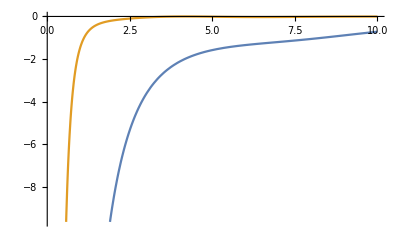

```mathematica
Plot[{Eigenvalues[hessian[tt, (1+gam)/2.]][[1]],Eigenvalues[hessian[tt,(1+gam)/2.]][[2]]},{tt,0.1,10}]
```

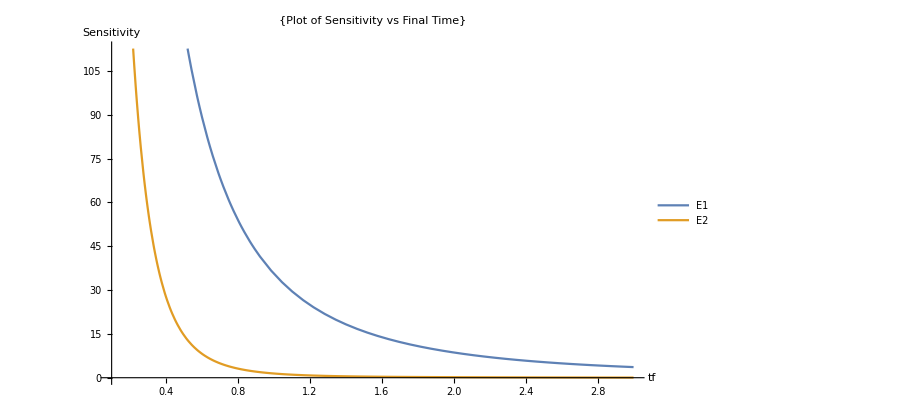

```mathematica
Plot[{Abs[Eigenvalues[hessian[tt, (1+gam)/2.]][[1]]],Abs[Eigenvalues[hessian[tt, (1+gam)/2.]][[2]]]},{tt,0.1,3},PlotLabel->{"Plot of Sensitivity vs Final Time"},PlotLegends->{"E1","E2"}, AxesLabel->{"tf","Sensitivity"}]
```

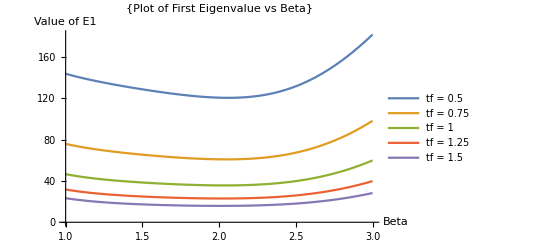

```mathematica
phess = Plot[{Abs[Eigenvalues[hessian[0.5, bbb]][[1]]],Abs[Eigenvalues[hessian[0.75, bbb]][[1]]],Abs[Eigenvalues[hessian[1., bbb]][[1]]],Abs[Eigenvalues[hessian[1.25, bbb]][[1]]],Abs[Eigenvalues[hessian[1.5, bbb]][[1]]]},{bbb,1.,3.},PlotLabel->{"Plot of First Eigenvalue vs Beta"},PlotLegends->{"tf = 0.5","tf = 0.75","tf = 1","tf = 1.25","tf = 1.5"}, AxesLabel->{"Beta","Value of E1"}]
```

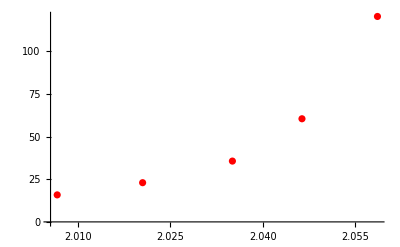

```mathematica
ppoint = ListPlot[{{2.05862,120.548},{2.04637,60.5168},{2.03508,35.686},{2.02051,23.0109},{2.00665,15.8519}},PlotStyle->Directive[Red,1]]
```

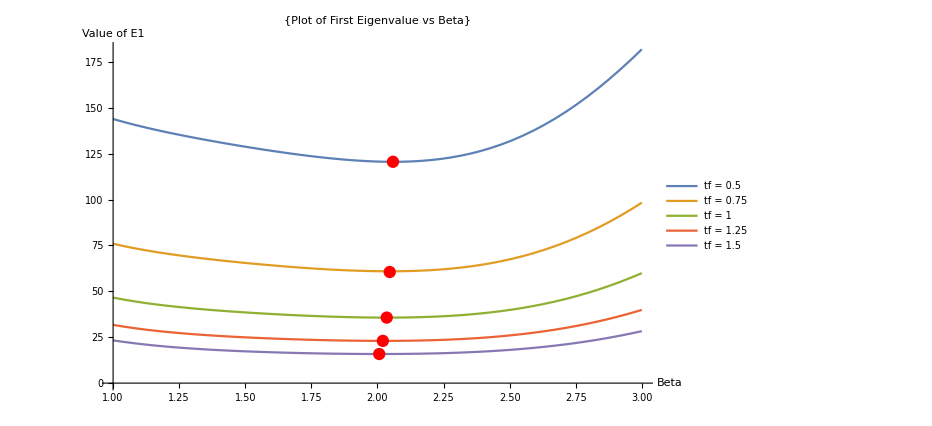

```mathematica
Show[phess,ppoint]
```

```mathematica
f[tff_,bbb_Real]:=Abs[Eigenvalues[hessian[tff, bbb]][[1]]]
```

```mathematica
FindMinimum[f[0.5,bbb],{bbb,2.1}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{120.548,{bbb→2.05862}}